# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Appendix A - Computer Programming in a Nutshell

## A.1 ONLINE TUTORIALS

Mathematica Basics: A 12-minute mini-introduction to Mathematica in general. If you don’t know how to do basic data entry in Mathematica, be sure to watch this tutorial. Even if you have used Mathematica before, you may learn some useful shortcuts. http://www.wolfram.com/broadcast/search.php?video=489

Hands-On Start to Mathematica: About an hour of material, comprised of short (10– 15 minute) videos illustrating various aspects of Mathematica. If you have the time, this will give you a comprehensive introduction. http://www.wolfram.com/broadcast/video.php?channel=135

Elementary Programming in Mathematica: A 12-minute introduction to the programming concepts in this appendix. If you don’t have the time for the previous tutorial, at least watch this one. http://www.wolfram.com/broadcast/search.php?video=409

An Elementary Introduction to the Wolfram Language: This assumes no background in programming. The sections most relevant to this textbook are 1–6, 13, 15, 23, 28, 40, and 47. http://www.wolfram.com/language/elementary-introduction/

Fast Introduction for Programmers: If you have prior programming experience, this brief tutorial will introduce you to the syntax and philosophy of Mathematica. 
http://www.wolfram.com/language/fast-introduction-for-programmers/

## A.2 ELEMENTS OF PROGRAMMING

```mathematica
(*this is a comment*)
```

## A.3 INPUT AND OUTPUT

```mathematica
1
2;
```

1

```mathematica
"One"
Print["Two ",3]
```

One

Two 3

### A.3.1 Entering special characters

```mathematica
π
```

```mathematica
Π
```

## A.4 MATH

### A.4.1 Variables

```mathematica
x=1;
```

```mathematica
x
```

1

#### Checking variable definition status

```mathematica
x=1;
```

```mathematica
Definition[x]
```

x=1

```mathematica
Definition[z]
```

Null

```mathematica
?x
```

Global`x

x=1

```mathematica
?z
```

Global`z

#### Numerical representations

#### Lists

```mathematica
x={1,2,3}
```

{1,2,3}

```mathematica
MatrixForm[x]
```

(1
2
3)

```mathematica
y={{11,12},{21,22}}
```

{{11,12},{21,22}}

```mathematica
MatrixForm[y]
```

(11 | 12
21 | 22)

```mathematica
x[[2]]
```

2

```mathematica
y[[2,1]]
```

21

```mathematica
x[[-1]]
```

3

```mathematica
Length[x]
```

3

```mathematica
AppendTo[x,10]
```

{1,2,3,10}

```mathematica
x
```

{1,2,3,10}

### A.4.2 Operators

```mathematica
a=2;
a+1
a+a
```

3

4

```mathematica
x={1,2,3}; y={10,20,30};
x+y
```

{11,22,33}

```mathematica
x*y
```

{10,40,90}

```mathematica
x.y
```

140

#### Alternatives to the exponentiation operator

#### Order of operations

```mathematica
y=a+x/b+x
```

```mathematica
y=(a+x)/(b+x)
```

#### Boolean operators

```mathematica
a=2;b=3;c=1;
a<b
```

True

```mathematica
a≤c
```

False

```mathematica
True&&True
True&&False
False&&True
False&&False
```

True

False

False

False

```mathematica
True||True
True||False
False||True
False||False
```

True

True

True

False

```mathematica
a=2;b=3;c=1;
(a<b)&&(b>c)
```

True

```mathematica
(a<b)||(a<c)
```

True

#### Assignment ≠ Equality

```mathematica
a=1;
a=a+1;
a=a+1;
a=a+2;
a
```

5

```mathematica
a=1;b=2;
a=b
a
```

2

2

```mathematica
a=1;b=2;
a==b
a
```

False

1

#### Combined assignment and arithmetic operators

```mathematica
x=1;dx=2;
x+=dx
```

3

```mathematica
x*=dx
```

6

```mathematica
++x
```

7

```mathematica
x 
x++ 
x
```

7

7

8

#### Significant figure calculations

```mathematica
x=100.;
y=0.01;
x+y
x*y
```

100.01

1.

```mathematica
x=SetPrecision[100.,3];
y=SetPrecision[0.01,2];
x+y
x*y
```

100.

1.

### A.4.3 Built-in mathematical functions

```mathematica
?Sin
```

Sin[z] gives the sine of z.

```mathematica
Definition[Sin]
```

Attributes[Sin]={Listable,NumericFunction,Protected}

```mathematica
Definition[Sine]
```

Null

### A.4.4 Defining your own functions

```mathematica
reportBottles[nBottles_]:=Print[nBottles," bottles of beer on the wall"];
```

```mathematica
reportBottles[5]
```

5 bottles of beer on the wall

```mathematica
f[x_]:=Module[
{a,b},(*list of local variables*)
a=2*x;(*calculation steps,each line terminated with semicolon*)
b=x^2;
a+b (*value returned by f[],note absence of semicolon*)
]
```

```mathematica
a=1;
f[a]
a
```

3

1

### A.4.5 Postfix function application

```mathematica
list={3,1,5,9,7};
Sort[list]
```

{1,3,5,7,9}

```mathematica
list//Sort
```

{1,3,5,7,9}

## A.5 LOOPS

```mathematica
Do[ reportBottles[i],{i,10,1,-1} ]
```

10 bottles of beer on the wall

9 bottles of beer on the wall

8 bottles of beer on the wall

7 bottles of beer on the wall

6 bottles of beer on the wall

5 bottles of beer on the wall

4 bottles of beer on the wall

3 bottles of beer on the wall

2 bottles of beer on the wall

1 bottles of beer on the wall

```mathematica
Do[ reportBottles[i],{i,1,3} ]
```

1 bottles of beer on the wall

2 bottles of beer on the wall

3 bottles of beer on the wall

```mathematica
Do[ reportBottles[i],{i,3} ]
```

1 bottles of beer on the wall

2 bottles of beer on the wall

3 bottles of beer on the wall

```mathematica
Do[ reportBottles["undefined number of"],{3} ]
```

undefined number of bottles of beer on the wall

undefined number of bottles of beer on the wall

undefined number of bottles of beer on the wall

### A.5.1 Loops implied by other functions

```mathematica
geometricSeries=Sum[(1/2)^n,{n,1,100}]
```

1267650600228229401496703205375/1267650600228229401496703205376

```mathematica
N[geometricSeries]
```

1.

### A.5.2 Loops that generate arrays

```mathematica
partialGeometricSeries=Table[
N[ Sum[(1/2)^n,{n,1,j}]],
{j,1,50}]
```

{0.5,0.75,0.875,0.9375,0.96875,0.984375,0.992188,0.996094,0.998047,0.999023,0.999512,0.999756,0.999878,0.999939,0.999969,0.999985,0.999992,0.999996,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## A.6 CONDITIONALS

```mathematica
assignPassFail[numberGrade_]:=If[(numberGrade>70),(*condition to test*)
"Pass",(*this second argument is evaluated if condition is true*)
"Fail" (*else this third argument is evaluated when it is false*)]
```

```mathematica
{assignPassFail[100],assignPassFail[50]}
```

{Pass,Fail}

### A.6.1 Conditional loops

```mathematica
n=1;
While[(n<4),
Print[n];
n++
]
```

1

2

3

## A.7 VISUALIZING YOUR DATA

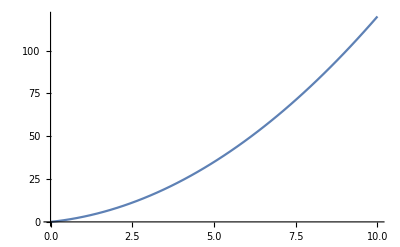

```mathematica
Plot[ f[x],{x,0,10}]
```

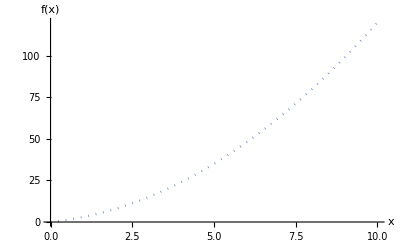

```mathematica
Plot[ f[x],{x,0,10},
AxesLabel->{"x","f(x)"},
PlotStyle->{Dotted} ]
```

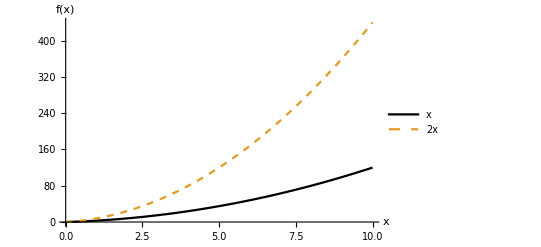

```mathematica
Plot[ {f[x],f[2*x]},{x,0,10},
AxesLabel->{"x","f(x)"},
PlotStyle->{Black,Dashed},
PlotLegends->{"x","2x"} ]
```

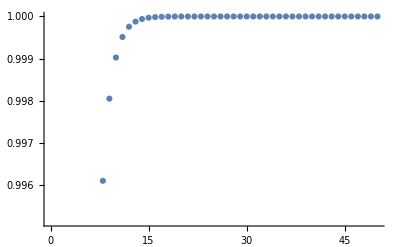

```mathematica
ListPlot[ partialGeometricSeries ]
```

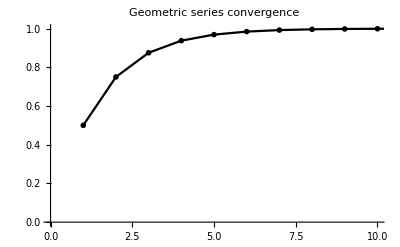

```mathematica
ListPlot[ partialGeometricSeries,
Joined->True,
PlotRange->{{0,10},{0,1}},
PlotLabel->"Geometric series convergence",
PlotTheme->"Monochrome"] (*theme used to generate figures in the book*)
```